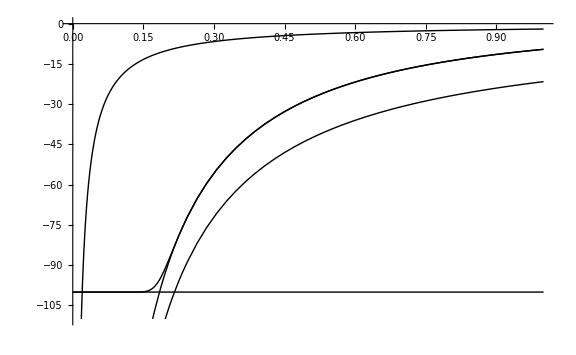
-Graphics-r/r_AUE/E_AU𝒩 = 101

```mathematica
Block[{
prec,Δ,
𝒩,Uc,
𝓀,rules,rule,n,
α,
f,g,
s,eqn,soln,
plt
},
prec=960;
Δ=SetPrecision[.1,prec];

𝒩=101;
Uc=SetPrecision[100.,prec];


rules=SetPrecision[{
{η->11.4,A->1.1750,γ0->0.7572,γ1->0.3223,γ2->2.044},
{η->10.8,A->1.1750,γ0->0.7572,γ1->0.3223,γ2->2.044},
{η->11.3,A->1.0000,  γ0->0.9500,γ1->0.0000,γ2->2.044},
{η->10.8,A->0.8918,γ0->0.9743,γ1->0.1586,γ2->0.1586}
},prec];
rule=rules[[4]];

f=Uc Sum[2/Uc((𝒩 α)/(6𝓀[0]) Sum[Binomial[n,i](D[𝓀[(6𝓀[0])/(𝒩 α)𝓇],{𝓇,i}]/.{𝓇->0}),{i,0,n}]-(n Uc)/2)((𝒩 α)/(6𝓀[0]) r)^(n-1)/(n!),{n,0,𝒩-1}];
g=-2/r 𝓀[r]+Exp[-(𝒩 α)/(6𝓀[0])r]f;

s=Collect[Series[g,{r,0,𝒩}],r,Together];
eqn=Assuming[{Uc>0,𝓀[0]>0},
D[s,{r,𝒩-1}]/.r->0//FullSimplify
];
𝓀[r_]=1+A η Exp[-γ0 r]+(1-A)η Exp[-γ1 r]-Exp[-γ2 r]/.rule;
α=Select[Block[{x=Solve[eqn==0,α]},Table[x[[n,1]][[2]],{n,1,Length[x]}]]//Chop,Positive]//Max;

Off[General::munfl];
plt=Plot[
{
Style[-Uc,Dashed,Thickness[Medium],Red],Style[-2/r,DotDashed,Thickness[Medium],Darker[Green]],Style[-2/r 𝓀[0],DotDashed,Thickness[Medium],Blue]
,Style[g,Purple],Style[-2/r 𝓀[r],Orange,Thickness[Large]]
}
,{r,0,1}
,WorkingPrecision->prec-10,PerformanceGoal->"Quality",ImageSize->Large
,PlotRange->{(-1-Δ)Uc,0}];
Labeled[plt,{r/Subscript[r, AU],"E/E_AU","𝒩 = "<>ToString[𝒩]},{Top,Left,Bottom}]//Print;
On[General::munfl];
]
```

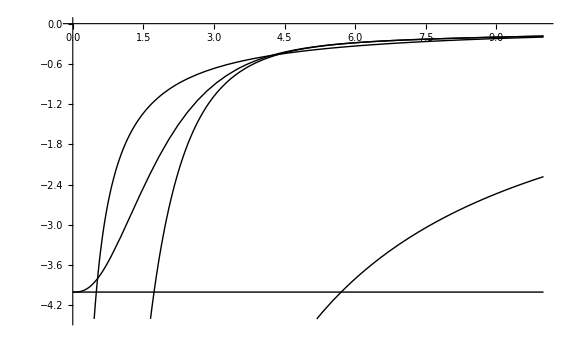
-Graphics-r/r_AUE/E_AU𝒩 = 3

```mathematica
Block[{
prec,Δ,
𝒩,Uc,
𝓀,rules,rule,n,
α,
f,g,
s,eqn,soln,
plt
},
prec=960;
Δ=SetPrecision[.1,prec];

𝒩=3;
Uc=SetPrecision[4.,prec];


rules=SetPrecision[{
{η->11.4,A->1.1750,γ0->0.7572,γ1->0.3223,γ2->2.044},
{η->10.8,A->1.1750,γ0->0.7572,γ1->0.3223,γ2->2.044},
{η->11.3,A->1.0000,  γ0->0.9500,γ1->0.0000,γ2->2.044},
{η->10.8,A->0.8918,γ0->0.9743,γ1->0.1586,γ2->0.1586}
},prec];
rule=rules[[1]];

f=2Sum[((𝒩 α)/(6𝓀[0]) Sum[Binomial[n,i](D[𝓀[(6𝓀[0])/(𝒩 α)𝓇],{𝓇,i}]/.{𝓇->0}),{i,0,n}]-(n Uc)/2)((𝒩 α)/(6𝓀[0])r)^(n-1)/(n!),{n,0,𝒩-1}];
g=-2/r 𝓀[r]+Exp[-(𝒩 α)/(6𝓀[0])r]f;

s=Collect[Series[g,{r,0,𝒩}],r,Together];
eqn=Assuming[{Uc>0,𝓀[0]>0},
D[s,{r,𝒩-1}]/.r->0//FullSimplify
];
𝓀[r_]=1+A η Exp[-γ0 r]+(1-A)η Exp[-γ1 r]-Exp[-γ2 r]/.rule;
α=Select[Block[{x=Solve[eqn==0,α]},Table[x[[n,1]][[2]],{n,1,Length[x]}]]//Chop,Positive]//Max;

Off[General::munfl];
plt=Plot[
{
Style[-Uc,Dashed,Thickness[Medium],Red],Style[-2/r,DotDashed,Thickness[Medium],Darker[Green]],Style[-2/r 𝓀[0],DotDashed,Thickness[Medium],Blue]
,Style[g,Purple],Style[-2/r 𝓀[r],Orange,Thickness[Large]]
}
,{r,0,10}
,WorkingPrecision->prec-10,PerformanceGoal->"Quality",ImageSize->Large
,PlotRange->{(-1-Δ)Uc,0}];
Labeled[plt,{r/Subscript[r, AU],"E/E_AU","𝒩 = "<>ToString[𝒩]},{Top,Left,Bottom}]//Print;
On[General::munfl];
]
```

```mathematica
Block[{
prec,Δ,
𝒩,Uc,
𝓀,rules,rule,n,
α,
f,g,
s,eqn,soln,
plt
},
𝒩=3;

f=2 Sum[((𝒩 α)/(6𝓀[0]) Sum[Binomial[n,i](D[𝓀[(6𝓀[0])/(𝒩 α)𝓇],{𝓇,i}]/.{𝓇->0}),{i,0,n}]-(n Uc)/2)((𝒩 α)/(6𝓀[0])r)^(n-1)/(n!),{n,0,𝒩-1}];
g=-2/r 𝓀[r]+Exp[-(𝒩 α)/(6𝓀[0])r]f;

s=Collect[Series[g,{r,0,𝒩}],r,Together];
eqn=Assuming[{Uc>0,𝓀[0]>0,A>0,η>1},
(D[s,{r,𝒩-1}]/.r->0)==0//FullSimplify
];
𝓀[r_]=1+A η Exp[-γ0 r]+(1-A)η Exp[-γ1 r]-Exp[-γ2 r];


Collect[g,{Exp[_],r},FullSimplify]//Print;
Assuming[{α>0,Uc>0},Collect[eqn,α,Expand[FullSimplify[#]]&]]

]
```

-2/r+(2 ⅇ^(-r γ2))/r-(2 A ⅇ^(-r γ0) η)/r+(2 (-1+A) ⅇ^(-r γ1) η)/r+ⅇ^(-(r α)/(2 ((1-A) η+A η))) (-Uc+α+2 γ2+(2 η)/r-2 (A γ0+γ1-A γ1) η+r (-α γ1-γ2^2+(α (-2 Uc+α+4 γ2))/(4 η)+γ1^2 η+A (γ0-γ1) (-α+(γ0+γ1) η)))

α^3+8 γ2^3 η^2-8 A γ0^3 η^3-8 γ1^3 η^3+8 A γ1^3 η^3+α^2 (-3 Uc+6 γ2-6 A γ0 η-6 γ1 η+6 A γ1 η)+α (-12 γ2^2 η+12 A γ0^2 η^2+12 γ1^2 η^2-12 A γ1^2 η^2)==0

```mathematica
Block[{
prec,Δ,
𝒩,Uc,
𝓀,rules,rule,n,
α,
f,g,
s,eqn,soln,
plt
},
𝒩=5;
Uc=3;

prec=20;
rules=SetPrecision[{
{η->11.4,A->1.1750,γ0->0.7572,γ1->0.3223,γ2->2.044},
{η->10.8,A->1.1750,γ0->0.7572,γ1->0.3223,γ2->2.044},
{η->11.3,A->1.0000,  γ0->0.9500,γ1->0.0000,γ2->2.044},
{η->10.8,A->0.8918,γ0->0.9743,γ1->0.1586,γ2->0.1586}
},prec];
rule=rules[[1]];

f=2Sum[((𝒩 α)/(6𝓀[0]) Sum[Binomial[n,i](D[𝓀[(6𝓀[0])/(𝒩 α)𝓇],{𝓇,i}]/.{𝓇->0}),{i,0,n}]-(n Uc)/2)((𝒩 α)/(6𝓀[0])r)^(n-1)/(n!),{n,0,𝒩-1}];
g=-2/r 𝓀[r]+Exp[-(𝒩 α)/(6𝓀[0])r]f;

s=Collect[Series[g,{r,0,𝒩}],r,Together];
eqn=Assuming[{Uc>0,𝓀[0]>0,A>0,η>1},
(D[s,{r,𝒩-1}]/.r->0)==0//FullSimplify
];
𝓀[r_]=1+A η Exp[-γ0 r]+(1-A)η Exp[-γ1 r]-Exp[-γ2 r];
eqn/.rule//Print;
α=Select[Block[{x=Solve[eqn/.rule,α]},Table[x[[n,1]][[2]],{n,1,Length[x]}]]//Chop,Positive]//Max;


Collect[g/.rule,{Exp[_],r},FullSimplify]//Print;

]
```

4.24877558343493952×10^9+25 α (-2.5101808033952904×10^7+5 α (156703.360359903738+5 α (2704.4347980276001+5 (-53.73423300000000189+α) α)))==0

-2/r+(2 ⅇ^(-2.0440000000000000391 r))/r-(26.79000000000000185 ⅇ^(-0.75719999999999998419 r))/r+(3.990000000000001137 ⅇ^(-0.3222999999999999754 r))/r+ⅇ^(-2.7975079558050036 r) (45.871770392354084+22.80000000000000071/r+42.404540626888852 r+23.25509410242034 r^2+7.233910995334191 r^3)